```mathematica
(*Plot the plane*)
w1=-3;
w2=1;
b=  2;
planeEquation[x1_,x2_]:=w1*x1+w2*x2+b;

(*Plot the plane and a light x1-x2 reference plane*)
Show[Plot3D[planeEquation[x1,x2],{x1,-5,5},{x2,-5,5},AxesLabel->{"x1","x2","wtx"},PlotStyle->Opacity[0.7,Blue],Boxed->True,PlotRange->{{-5,5},{-5,5},{-10,10}},Lighting->"Neutral"],Plot3D[0,{x1,-5,5},{x2,-5,5},PlotStyle->Opacity[0.5,Gray],Mesh->None]]
```

-Graphics3D-

```mathematica
(*Define the plane function wtx*)
wtx[x1_,x2_]:=w1*x1+w2*x2+b

(*Define the decision boundary where wtx=0,solving for x2*)
x2Sol[x1_]:=(-w1*x1-b)/w2

(*Define the activation function (Sigmoid)*)
sigmoid[z_]:=1/(1+Exp[-z])

(*Plot the decision boundary*)
decisionBoundaryPlot=Plot[x2Sol[x1],{x1,-5,5},PlotStyle->{Black},AxesLabel->{"x1","x2"},PlotLabel->"Decision Boundary wtx[x1, x2] = 0",GridLines->Automatic];

(*Plot the surface of the activation function sigmoid(wtx)*)
sigmoid_p =activationSurfacePlot=Plot3D[sigmoid[wtx[x1,x2]],{x1,-5,5},{x2,-5,5},PlotStyle->Directive[Opacity[0.7],Blue],AxesLabel->{"x1","x2","a"},PlotLabel->"Activation Function Sigmoid(wtx[x1, x2])",MeshStyle->Red,ColorFunction->"Rainbow",Boxed->True];

(*Show both plots*)
GraphicsRow[{decisionBoundaryPlot,activationSurfacePlot}]
```

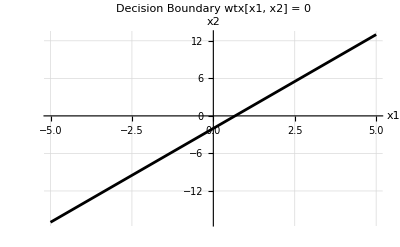

```mathematica
(*Define weight vector w and variable vector x*)w={b,w1,w2};
x={1,_x1,_x2};

(*Display the vectors*)
w
x
dotProduct=w.x
```

{2,-3,1}

{1,_x1,_x2}

2-3 _x1+_x2

```mathematica
(*Define the plane function wtx*)
wtx[x1_,x2_]:=w1*x1+w2*x2+b

(*Define the decision boundary where wtx=0,solving for x2*)
x2Sol[x1_]:=(-w1*x1-b)/w2

z[x1_,x2_]:=Tanh[wtx[x1,x2]] (*Example activation function*)

(*Plot the decision boundary*)
decisionBoundaryPlot=Plot[x2Sol[x1],{x1,-5,5},PlotStyle->{Black},AxesLabel->{"x1","x2"},PlotLabel->"Decision Boundary wtx[x1, x2] = 0",GridLines->Automatic];

(*Plot the surface of the activation function sigmoid(wtx)*)
tanh_d =Plot3D[z[x1,x2],{x1,-10,10},{x2,-10,10},PlotStyle->Directive[Opacity[0.7],Blue],AxesLabel->{"x1","x2","a"},PlotLabel->"Activation Function Tanh(wtx[x1, x2])",MeshStyle->Red,ColorFunction->"Rainbow",Boxed->True]

sigmoid[z_]:=1/(1+Exp[-z])
sigmoid_p =Plot3D[sigmoid[wtx[x1,x2]],{x1,-5,5},{x2,-5,5},PlotStyle->Directive[Opacity[0.7],Blue],AxesLabel->{"x1","x2","a"},PlotLabel->"Activation Function Sigmoid(wtx[x1, x2])",MeshStyle->Red,ColorFunction->"Rainbow",Boxed->True]

decisionBoundaryPlot=Plot[x2Sol[x1],{x1,-5,5},PlotStyle->{Black},AxesLabel->{"x1","x2"},PlotLabel->"Decision Boundary wtx[x1, x2] = 0",GridLines->Automatic];

GraphicsRow[{sigmoid_p, tanh_d , decisionBoundaryPlot}]
```

-Graphics3D-

-Graphics3D-

-Graphics-